-ⅈ

ⅈ

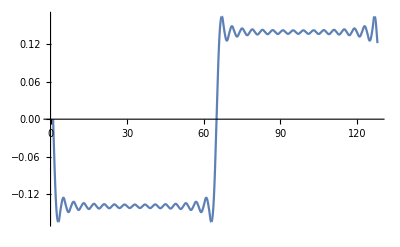

```mathematica
n=128;
sr=1000;
dt=1/sr;
df=sr/n;
freqs=Range[-n/2,n/2-1]/(n*dt)//N;
h=32;
spectrum=RotateRight[Table[If[k==0||Abs[k]>h,0,-I/k],{k,-n/2,n/2-1}],n/2];
spectrumSqr=RotateRight[Table[If[EvenQ[k]||k==0||Abs[k]>h,0,-I/k],{k,-n/2,n/2-1}],n/2];
fft =InverseFourier[spectrumSqr];
spectrumSqr[[2]]
spectrumSqr[[n]]
ListLinePlot[Re[fft],PlotRange->Full,InterpolationOrder->2]
(* Transpose[ListA,ListB] is another option *)
(*
ListPlot[{MapThread[List,{RotateRight[freqs,n/2],Re[fft]}],MapThread[List,{RotateRight[freqs,n/2],Im[fft]}]},PlotRange->Full,Filling->Axis]
*)
```